(1+x)^2+y^2

(-1+x)^2+y^2

√((-1+x)^2+y^2) ((1+x)^2+y^2)

If[y>0,(ArcTan[y-y1,x-x1] a1+ArcTan[y-y2,x-x2] a2)/(a1+a2),(ArcTan[-y-y1,x-x1] a1+ArcTan[-y-y2,x-x2] a2)/(a1+a2)]

1

1/2

2

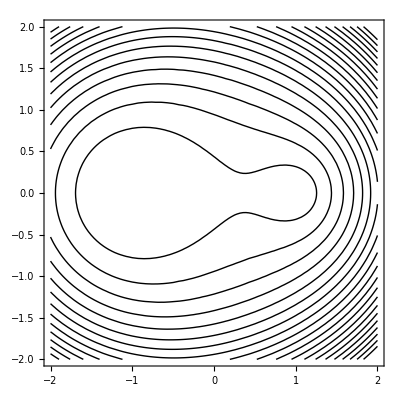

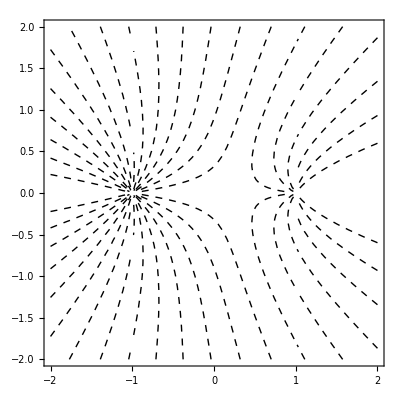

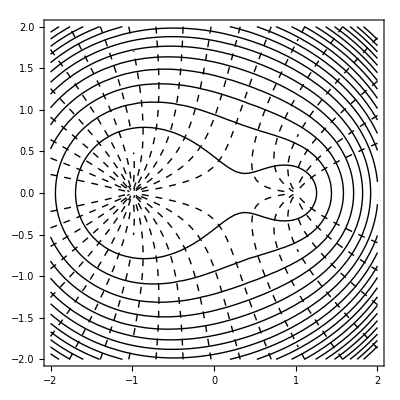

```mathematica
Clear[x1,x2,y1,y2,x,y,f,g]

x1 = -1;
y1 = 0 ; 
x2 = 1;
y2 = 0 ; 

d1 = (x-x1)^2 + (y-y1)^2
d2 = (x-x2)^2 + (y-y2)^2

f = d1^a1 d2^a2
g[x_,y_] = If[y>0,
(ArcTan[(y-y1),(x-x1)] a1 + ArcTan[(y-y2),(x-x2)] a2)/(a1+a2),
(ArcTan[(-y-y1),(x-x1)] a1 + ArcTan[(-y-y2),(x-x2)] a2)/(a1+a2)
]




a1 = 2/2
a2 = 1/2

gg = 2
c1=ContourPlot[f,{x,-gg,gg},{y,-gg,gg},Contours->20,ContourShading->None]
c2=ContourPlot[g[x,y],{x,-gg,gg},{y,-gg,gg},Contours->20,ContourShading->None, ContourStyle->Dashed]
Show[c1,c2]
```